```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin hourly price: Recent (≥ 2024) data - bitstamp.com.

- Bitcoin circulating supply: https://www.blockchain.com/charts/total-bitcoins.

## In This Notebook

LPPLS model implementation (2026 ed.).

```mathematica
base=DirectoryName[NotebookFileName[]];
lastPriceDate=DateString[Yesterday,"ISODate"]
```

2026-04-14

```mathematica
hourlyPricesUrl="https://www.cryptodatadownload.com/cdd/Bitstamp_BTCUSD_1h.csv";
prices =Import[hourlyPricesUrl, HeaderLines->1]
```

```mathematica
(* First price date: *)
firstDownloadedDateTime=prices[[-1]][[2]];
{firstDownloadedDate,firstDownloadedTime}=StringSplit[firstDownloadedDateTime];
firstPriceDate=firstDownloadedDate
```

2018-05-15

```mathematica
(* Some freshness checks: *)
lastDownloadedDateTime=prices[[2]][[2]];
{lastDownloadedDate, lastDownloadedTime}=StringSplit[lastDownloadedDateTime]
{DateString[DatePlus[lastDownloadedDate, -1], "ISODate"]==lastPriceDate, lastDownloadedTime=="00:00:00"}
```

{2026-04-15,00:00:00}

{True,True}

```mathematica
closingPrices={#[[1]],#[[7]]}&/@prices
```

```mathematica
(* Filter non-numerical values *)
closingPricesFilter=Select[closingPrices, NumberQ[#[[2]]]&]
```

```mathematica
(* Hourly data *)
hourlyPrices=SortBy[closingPricesFilter, First]
```

```mathematica
Length[hourlyPrices]
```

69363

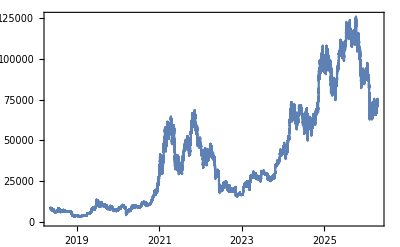

```mathematica
DateListPlot[hourlyPrices,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
Export[base<>"csv/Bitcoin_price-hourly-"<>StringDelete[firstPriceDate, "-"]<>"-"<>StringDelete[lastPriceDate, "-"]<>".csv",hourlyPrices]
```

/Users/mauro/Projects/Bitcoin/csv/Bitcoin_price-hourly-20180515-20260414.csv

```mathematica
(* Convert to market capitalization, using circulating supply data, from blockchain.info *)
(* Load circulating supply data: https://www.blockchain.com/charts/total-bitcoins *)
supplyJsonData = Import["https://api.blockchain.info/charts/total-bitcoins?timespan=all&sampled=true&metadata=false&daysAverageString=1d&cors=true&format=json"];
```

```mathematica
supplyJson=supplyJsonData[[6]][[2]]
```

```mathematica
supplyTs=supplyJson[[All, 1]][[All,2]];
supplyQuantity=supplyJson[[All, 2]][[All,2]];
```

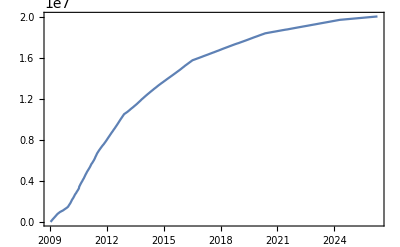

```mathematica
supplyTimestamps=MapThread[{#1, #2}&,{supplyTs, supplyQuantity}];
DateListPlot[supplyTimestamps,DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Create an interpolating function from it *)
supplyFunction=Block[{},Off[ InterpolatingFunction::dmval];Interpolation[supplyTimestamps]]
```

InterpolatingFunction[…]

```mathematica
{supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}
```

{1231568277,1776098001}

```mathematica
{hourlyPrices[[1]][[1]],hourlyPrices[[-1]][[1]]}
```

{1526364000,1776211200}

```mathematica
{supplyFunction[hourlyPrices[[1]][[1]]], supplyFunction[hourlyPrices[[-3]][[1]]]}
```

{1.70343×10^7,2.00159×10^7}

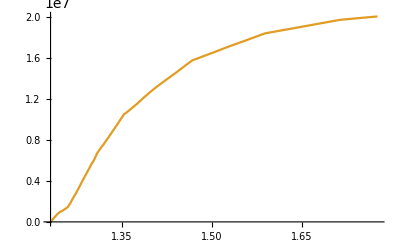

```mathematica
Plot[{,supplyFunction[i]}, {i, supplyTimestamps[[1]][[1]], supplyTimestamps[[-1]][[1]]}]
```

```mathematica
(* Generate hourly market capitalization data *)
hourlyMarketCap={#[[1]], #[[2]]*supplyFunction[#[[1]]]}&/@hourlyPrices
```

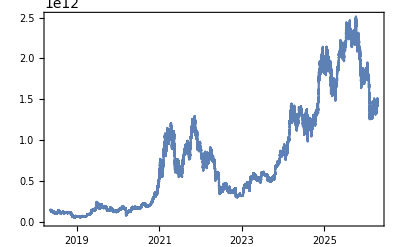

```mathematica
DateListPlot[hourlyMarketCap, DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Use the Log Market Cap *)
logMarketCap= {#[[1]], Log[#[[2]]]}&/@hourlyMarketCap
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2026 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2025-11-23", lastPriceDate}, {"2026-02-06", lastPriceDate}}
```

{{2025-11-23,2026-04-14},{2026-02-06,2026-04-14}}

```mathematica
bubbleN=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1763848800,1776117600},{1770328800,1776117600}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{142,67}

```mathematica
bubbles=Table[Select[logMarketCap,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, bubbleN}];
#[[1]]&/@bubbles
```

{{1763848800,28.1594},{1770328800,27.8738}}

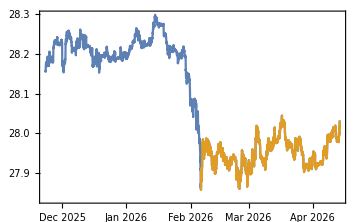

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{2.68346,0.395805},{1.71246,0.934188}}

```mathematica
Length/@bubblesScaled
```

{3389,1589}

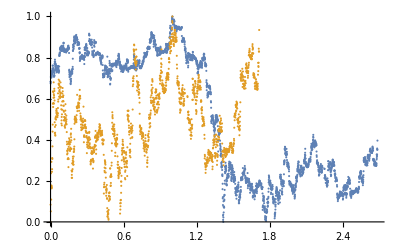

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
ListPlot[bubblesScaled]
```

```mathematica
(* Export bubbles data: *)
bubbleScaledCsvs=MapIndexed[Export[base<>"csv/bubbleScaled-Bitcoin-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,bubblesScaled]
```

{/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Bitcoin-1.tsv,/Users/mauro/Projects/Bitcoin/csv/bubbleScaled-Bitcoin-2.tsv}

```mathematica
(* Our "goodness of fit" control parameter. The smaller the better. i.e. stricter hypothesis testing will be. *)
(* Empirically, spans greater than 0.1 indicate that our prediction is not very reliable / trustworthy. *)bestSpan=0.09
```

0.09

```mathematica
(* Get params from R: *)
rInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@bubbleScaledCsvs;
```

```mathematica
rRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@rInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
rParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@rRuns
```

{{17.5662,3365.88},{17.6651,1565.77}}

```mathematica
(* {RSS, SE, SE of the fit}: *)
rErrors=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-6;;;;2]]&/@rRuns
```

{{7.03939,0.0457388,0.00312286},{9.93405,0.079679,0.00798421}}

```mathematica
(* Use Loess: *)
LoessR=ResourceFunction["Loess"]
```

```mathematica
bestFits = LoessR[#, Scaled[bestSpan], #[[All, 1]], {InterpolationOrder-> 1}]&/@bubblesScaled;
```

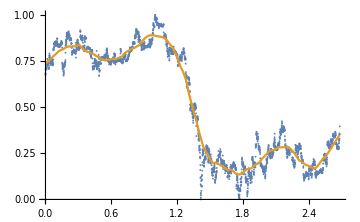
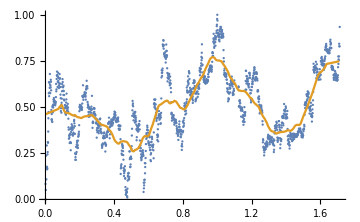

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, Scaled[bestSpan], t ]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, bubbleN}];
```

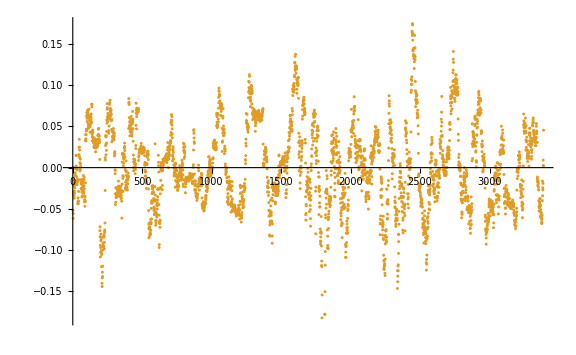
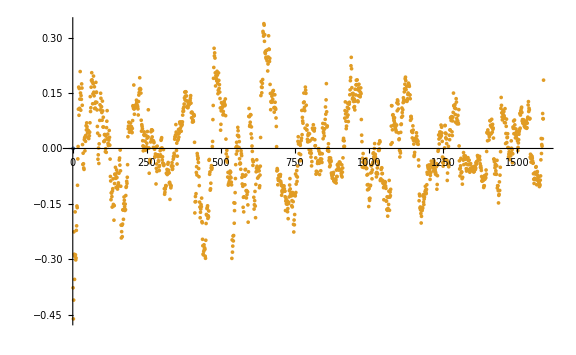

```mathematica
(* Plot residuals: *)
ListPlot[{{0,0},#}, ImageSize->Large]&/@ℛs
```

```mathematica
(* Standard deviations: *)
stdDevℛs=StandardDeviation /@ℛs
```

{0.0523221,0.106733}

```mathematica
(* Standardized residuals: *)
stdℛs = MapThread[#1/#2&,{ℛs, stdDevℛs}];
```

```mathematica
(* RSS: *)
ℛsSS =Total[#^2]&/@ℛs
```

{9.27517,18.0907}

```mathematica
(* Larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[1]]]&,{ℛsSS,rErrors}]
```

{9.27517 > 7.03939,18.0907 > 9.93405}

```mathematica
(* Residual Standard Error(s): *)
ℛsSEs=MapThread[√(Total[#1^2]/(Length[#1]-#2[[1]]))&,{ℛs,rParams}]
```

{0.052451,0.107298}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.052451 > 0.0457388,0.107298 > 0.079679}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(Length[#1]-#2[[1]]))&,{ℛs,rParams, rErrors}]
```

{0.0456941,0.0795113}

```mathematica
ℛsSEs=MapThread[√(Total[#1^2]/(#2[[2]]))&,{ℛs,rParams}]
```

{0.0524942,0.107489}

```mathematica
(* Slightly larger than in R: *)
MapThread[ToString[#1]<>" > "<>ToString[#2[[2]]]&,{ℛsSEs,rErrors}]
```

{0.0524942 > 0.0457388,0.107489 > 0.079679}

```mathematica
(* Comparing formulas: *)
MapThread[√((#3[[1]])/(#2[[2]]))&,{ℛs,rParams, rErrors}]
```

{0.0457318,0.0796526}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
numParams=7;
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Select first bubble for fitting: *)
bubble=1
```

```mathematica
(* Select last bubble for fitting: *)
bubble=bubbleN
```

2

```mathematica
(* Use the selected bubble: *)
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
(* Use the params for the selected bubble: *)
{estimatedNParams, effectiveDfs}=rParams[[bubble]]
```

{17.6651,1565.77}

```mathematica
(* Profiling over 0.1 < m < 1, 3 < ω < 14 and 1. < tc < 2 months in the future *)
minM=0.1;
maxM=1;
minω=3;
maxω=14;
months=2;
```

```mathematica
(* Try to estimate all the params using log-likelihood: *)
(* Define `months` in the future scaled interval endpoint: *)
bubbleScaled[[-1]][[1]]
maxTc=bubbleScaled[[-1]][[1]]+(bubblesDays[[bubble]]+30 months)/bubblesDays[[bubble]]//N
```

1.71246

3.60798

```mathematica
(* Define 3 days resolution scaled interval step: *)
stepTc=3/bubblesDays[[bubble]]//N
```

0.0447761

```mathematica
(* Define 3 days resolution scaled initial time step *)
stepTi=3/bubblesDays[[bubble]]//N
```

0.0447761

```mathematica
(* Slow. Shortcut below *)
Now[]
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[ParallelTable[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
RSS=Total[ℛ^2],
RSS/(Length[ℛ]-numParams),
StandardDeviation[ℛ],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,minM,maxM,1./10}, {ω,minω,maxω,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, maxTc,stepTc}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], RSS-> bestFit[[6]],ℛerror-> bestFit[[7]], ℛσ-> bestFit[[8]],LL-> bestFit[[9]]},bestFit[[5]]], {t1, Range[0,1/2+stepTi, stepTi]}]//AbsoluteTiming
```

Wed 15 Apr 2026 08:09:05GMT+2[]

{5017.51,{{a→1.18096,b→-0.711077,c→0.0170838,d→0.00092092,T_1→0.,tc→1.71256,m→0.1,ω→13.3,RSS→46.0836,ℛerror→0.02913,ℛσ→0.170352,LL→3341.42,ρ→0.983529,σ→-0.0307814,μ→2.68944×10^-18},{a→1.16929,b→-0.697782,c→0.0179021,d→0.00334609,T_1→0.0447761,tc→1.71256,m→0.1,ω→13.3,RSS→44.5159,ℛerror→0.0289252,ℛσ→0.169744,LL→3336.63,ρ→0.9863,σ→-0.027992,μ→-1.3684×10^-17},{a→1.21242,b→-0.747303,c→0.00978959,d→-0.00107709,T_1→0.0895522,tc→1.71256,m→0.1,ω→13.3,RSS→43.4534,ℛerror→0.029027,ℛσ→0.170033,LL→3249.63,ρ→0.986441,σ→-0.0278959,μ→-3.4591×10^-18},{a→1.25363,b→-0.794747,c→0.00475026,d→-0.020812,T_1→0.134328,tc→1.71256,m→0.1,ω→12.4,RSS→42.6329,ℛerror→0.029301,ℛσ→0.170823,LL→3165.43,ρ→0.986685,σ→-0.0277739,μ→6.22558×10^-18},{a→1.21263,b→-0.747426,c→0.00976151,d→-0.00371689,T_1→0.179104,tc→1.71256,m→0.1,ω→13.3,RSS→42.4371,ℛerror→0.0300334,ℛσ→0.172935,LL→3085.69,ρ→0.986961,σ→-0.0278259,μ→-9.27003×10^-18},{a→1.21146,b→-0.746099,c→0.0103891,d→-0.00322163,T_1→0.223881,tc→1.71256,m→0.1,ω→13.3,RSS→41.9776,ℛerror→0.0306182,ℛσ→0.174599,LL→2990.95,ρ→0.987274,σ→-0.0277559,μ→1.577×10^-17},{a→1.24284,b→-0.782555,c→0.00621066,d→0.00224891,T_1→0.268657,tc→1.71256,m→0.1,ω→13.3,RSS→41.4892,ℛerror→0.0312183,ℛσ→0.17629,LL→2890.48,ρ→0.987467,σ→-0.0278129,μ→-5.52633×10^-18},{a→1.24297,b→-0.782696,c→0.00593292,d→0.00223248,T_1→0.313433,tc→1.71256,m→0.1,ω→13.3,RSS→41.4016,ℛerror→0.0321691,ℛσ→0.178941,LL→2809.56,ρ→0.988051,σ→-0.0275691,μ→-1.12373×10^-17},{a→1.21102,b→-0.745421,c→0.00419789,d→-0.000987443,T_1→0.358209,tc→1.71256,m→0.1,ω→13.4,RSS→40.955,ℛerror→0.0328956,ℛσ→0.180936,LL→2711.13,ρ→0.988079,σ→-0.027843,μ→-4.94917×10^-18},{a→1.19795,b→-0.730135,c→0.0026989,d→-0.00333568,T_1→0.402985,tc→1.71256,m→0.1,ω→13.4,RSS→40.8634,ℛerror→0.033968,ℛσ→0.183846,LL→2610.14,ρ→0.988361,σ→-0.0279563,μ→8.58397×10^-18},{a→1.7064,b→-1.29512,c→0.104188,d→-0.218882,T_1→0.447761,tc→1.75734,m→0.1,ω→3.9,RSS→17.5242,ℛerror→0.015094,ℛσ→0.122541,LL→2534.15,ρ→0.973321,σ→-0.0281049,μ→-1.43585×10^-17},{a→1.62307,b→-1.20026,c→0.101506,d→-0.207137,T_1→0.492537,tc→1.75734,m→0.1,ω→3.9,RSS→16.5723,ℛerror→0.0148099,ℛσ→0.121371,LL→2449.54,ρ→0.972649,σ→-0.0281793,μ→4.46041×10^-18},{a→1.684,b→-1.26982,c→0.102256,d→-0.215871,T_1→0.537313,tc→1.75734,m→0.1,ω→3.9,RSS→15.8725,ℛerror→0.0147377,ℛσ→0.121062,LL→2360.57,ρ→0.972858,σ→-0.0280011,μ→-9.78502×10^-19}}}

```mathematica
(* Shortcut: *)
fits=;
```

```mathematica
(* Timing in minutes: *)
fits[[1]]/60
```

83.6251

```mathematica
fits=fits[[2]];
```

```mathematica
fits[[All,{5,6,11,12}]]//TableForm
```

T_1→0. | tc→1.71256 | ℛσ→0.170352 | LL→3341.42
T_1→0.0447761 | tc→1.71256 | ℛσ→0.169744 | LL→3336.63
T_1→0.0895522 | tc→1.71256 | ℛσ→0.170033 | LL→3249.63
T_1→0.134328 | tc→1.71256 | ℛσ→0.170823 | LL→3165.43
T_1→0.179104 | tc→1.71256 | ℛσ→0.172935 | LL→3085.69
T_1→0.223881 | tc→1.71256 | ℛσ→0.174599 | LL→2990.95
T_1→0.268657 | tc→1.71256 | ℛσ→0.17629 | LL→2890.48
T_1→0.313433 | tc→1.71256 | ℛσ→0.178941 | LL→2809.56
T_1→0.358209 | tc→1.71256 | ℛσ→0.180936 | LL→2711.13
T_1→0.402985 | tc→1.71256 | ℛσ→0.183846 | LL→2610.14
T_1→0.447761 | tc→1.75734 | ℛσ→0.122541 | LL→2534.15
T_1→0.492537 | tc→1.75734 | ℛσ→0.121371 | LL→2449.54
T_1→0.537313 | tc→1.75734 | ℛσ→0.121062 | LL→2360.57

```mathematica
(* Average tc: *)
meanTc=Total[fits[[All,6]][[All,2]]]/Length[fits]
```

1.72289

```mathematica
minTc=Min[fits[[All,6]][[All,2]]]
maxTc=Max[fits[[All,6]][[All,2]]]
```

1.71256

1.75734

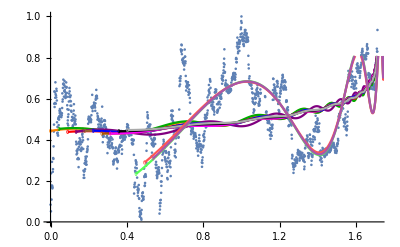

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black, Lighter[Gray], Lighter[Green], Lighter[Red], Lighter[Purple], Lighter[Brown], Lighter[Blue],Lighter[Orange]};
circles=Table[{colors[[Mod[i, Length[colors]]+1]],Thickness[0.0012],Circle[{i stepTi,lpplsModel/.fits[[i+1]]/.ti-> i stepTi},{0.005,0.0085}]}, {i, 0,Length[fits]-1}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>i stepTi,Evaluate[lpplsModel/.fits[[i+1]]],""], {i,0,Length[fits]-1}], {ti, 0, maxTc}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* 4. Rejection criteria: See if the residuals errors of the fits (ℛerror field) are below the 95% of the simulated (standardized) RSSs: *)
T1s=Subscript[T, 1]/.fits
ℛerrors=ℛerror/.fits
RSSs=RSS/.fits
ℛσs=ℛσ/.fits
```

{0.,0.0447761,0.0895522,0.134328,0.179104,0.223881,0.268657,0.313433,0.358209,0.402985,0.447761,0.492537,0.537313}

{0.02913,0.0289252,0.029027,0.029301,0.0300334,0.0306182,0.0312183,0.0321691,0.0328956,0.033968,0.015094,0.0148099,0.0147377}

{46.0836,44.5159,43.4534,42.6329,42.4371,41.9776,41.4892,41.4016,40.955,40.8634,17.5242,16.5723,15.8725}

{0.170352,0.169744,0.170033,0.170823,0.172935,0.174599,0.17629,0.178941,0.180936,0.183846,0.122541,0.121371,0.121062}

```mathematica
(* Only last bubble *)
npBestFit=bestFits[[bubble]];
```

```mathematica
nPℓ=Length[npBestFit];
nPℓ
```

1589

```mathematica
1493
```

1493

```mathematica
(* Plot of the residuals of the non-parametric fit vs the residuals of the parametric fit: *)
(* Non-parametric residuals: *)
npℛs=ℛs[[bubble]];
```

```mathematica
(* Parametric residuals: *)
fullFit[t_]:=lpplsModel/.fits[[1]]/.ti-> t
pℛs=Table[bubbleScaled[[i]][[2]]-fullFit[bubbleScaled[[i]][[1]]],{i,1,Length[bubbleScaled]}];
```

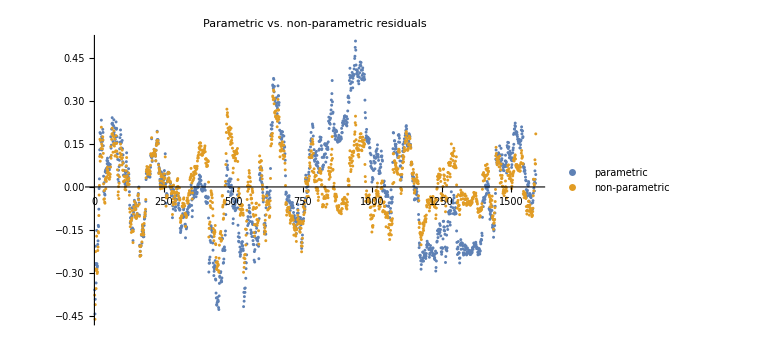

```mathematica
ListPlot[{pℛs,npℛs}, ImageSize->Large, {PlotLabel-> "Parametric vs. non-parametric residuals", PlotLegends->{"parametric","non-parametric"}}]
```

```mathematica
(* RSSs: *)
Total[#^2]&/@{npℛs, pℛs}
```

{18.0907,46.0836}

```mathematica
(* Residual Standard Errors: *)
{√(Total[npℛs^2]/effectiveDfs),√(Total[pℛs^2]/(Length[pℛs]-numParams)) }
```

{0.107489,0.170675}

```mathematica
(* Mean residual squared error: *)
{Total[npℛs^2]/effectiveDfs,Total[pℛs^2]/(Length[pℛs]-numParams) }
```

{0.0115539,0.02913}

```mathematica
selN=Length[T1s];
selN
```

13

```mathematica
selNpBestFit=Table[npBestFit[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selNpBestFit
```

{1589,1518,1447,1376,1305,1234,1163,1091,1020,949,878,807,736}

```mathematica
selBubbleScaled2=Table[bubbleScaled[[Floor[nPℓ T1s[[i]]+1];;]], {i,1,selN}];
```

```mathematica
Length/@selBubbleScaled2
```

{1589,1518,1447,1376,1305,1234,1163,1091,1020,949,878,807,736}

```mathematica
(* Export selected bubbles: *)
selBubbleScaledCsvs=MapIndexed[Export[base<>"csv/selBubbleScaled-Bitcoin-"<>ToString[First[#2]]<>".tsv", Join[{{"time","value"}},#1]]&,selBubbleScaled2];
```

```mathematica
selBubbleScaled=#[[All,2]]&/@selBubbleScaled2;
```

```mathematica
selNpℛs=Table[selBubbleScaled[[i]]-selNpBestFit[[i]], {i, 1,selN}];
```

```mathematica
(* Structural checks: *)
Length/@selNpℛs
```

{1589,1518,1447,1376,1305,1234,1163,1091,1020,949,878,807,736}

```mathematica
selBubbleScaled[[1]][[1]]==bubbleScaled[[1]][[2]]
selNpBestFit[[1]][[1]]==npBestFit[[1]]
selNpℛs[[1]][[1]]==ℛs[[bubble]][[1]]
```

True

True

True

```mathematica
(* Magnitude of the parametric residual fits: *)
ℛerrors
```

{0.02913,0.0289252,0.029027,0.029301,0.0300334,0.0306182,0.0312183,0.0321691,0.0328956,0.033968,0.015094,0.0148099,0.0147377}

```mathematica
RSSs
```

{46.0836,44.5159,43.4534,42.6329,42.4371,41.9776,41.4892,41.4016,40.955,40.8634,17.5242,16.5723,15.8725}

```mathematica
(* For each selection, do the simulations, and compute all the statistics: *)
(* Standard deviations: *)
selStdDevℛs=StandardDeviation[#]& /@selNpℛs
```

{0.106733,0.103012,0.10332,0.102693,0.103926,0.105916,0.106208,0.0987354,0.0975162,0.0968594,0.086333,0.0828017,0.0849367}

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
selEstimatedAR1Models=FindProcessParameters[#,ar1Process]&/@selNpℛs
```

{{ρ→0.95635,σ→-0.0311801,μ→0.0000116482},{ρ→0.960821,σ→-0.0285424,μ→3.02352×10^-6},{ρ→0.962173,σ→-0.0281387,μ→-0.0000380058},{ρ→0.961448,σ→-0.0282291,μ→0.0000370679},{ρ→0.96304,σ→-0.0279827,μ→-0.0000466083},{ρ→0.96368,σ→-0.0282743,μ→0.0000315693},{ρ→0.963668,σ→-0.0283562,μ→-0.0000992401},{ρ→0.959135,σ→-0.0279243,μ→-0.0000165735},{ρ→0.960155,σ→-0.0272393,μ→0.0000618149},{ρ→0.961803,σ→-0.0265005,μ→0.000184342},{ρ→0.953968,σ→-0.0258773,μ→-0.000148746},{ρ→0.951108,σ→-0.0255583,μ→0.000146808},{ρ→0.955095,σ→-0.0251496,μ→0.0000697262}}

```mathematica
(* Compute the log-likelihood of the fit *)
selEstimatedProcesses=ar1Process/.#&/@selEstimatedAR1Models
logLikelihoods=Table[LogLikelihood[selEstimatedProcesses[[i]],selNpℛs[[i]]], {i, Length[T1s]}]
```

{ARProcess[0.0000116482,{0.95635},0.0009722],ARProcess[3.02352×10^-6,{0.960821},0.00081467],ARProcess[-0.0000380058,{0.962173},0.000791786],ARProcess[0.0000370679,{0.961448},0.000796879],ARProcess[-0.0000466083,{0.96304},0.00078303],ARProcess[0.0000315693,{0.96368},0.000799436],ARProcess[-0.0000992401,{0.963668},0.000804072],ARProcess[-0.0000165735,{0.959135},0.000779766],ARProcess[0.0000618149,{0.960155},0.000741981],ARProcess[0.000184342,{0.961803},0.000702274],ARProcess[-0.000148746,{0.953968},0.000669635],ARProcess[0.000146808,{0.951108},0.000653225],ARProcess[0.0000697262,{0.955095},0.000632502]}

{3337.82,3274.24,3135.29,2982.71,2834.48,2667.96,2518.02,2376.33,2247.76,2140.77,1993.18,1842.65,1695.38}

```mathematica
(* Step 2: Characterize error variance. *)
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
selNPointss=Length/@selNpℛs;
nSims=1000;
selSims=ParallelTable[RandomFunction[selEstimatedProcesses[[i]],{0,selNPointss[[i]]-1},nSims], {i,selN}];
selNpℛsPlots=ParallelTable[MapThread[{#1,#2}&,{Range[0,selNPointss[[i]]-1],selNpℛs[[i]][[;;selNPointss[[i]]]]}], {i,selN}];
selPaths=#["Paths"]&/@selSims;
```

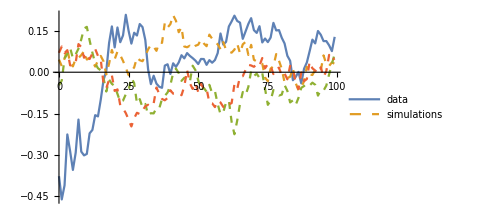
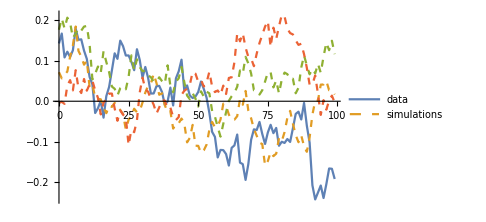
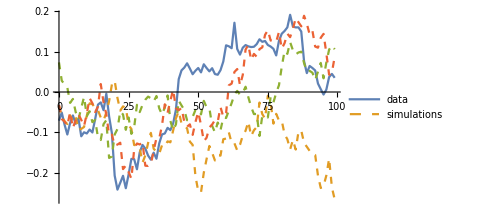
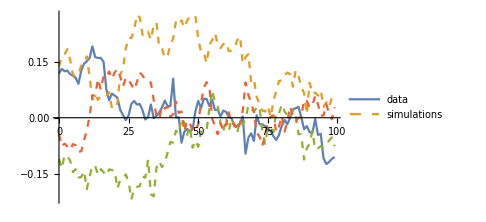
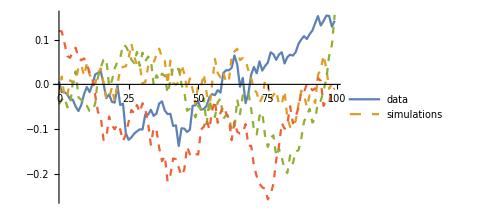
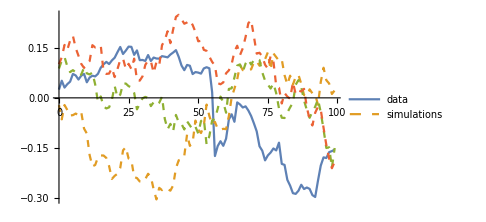
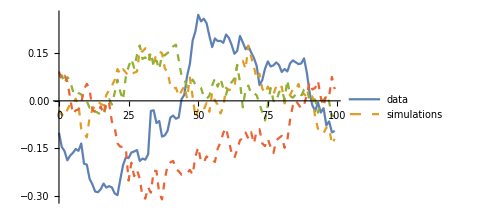
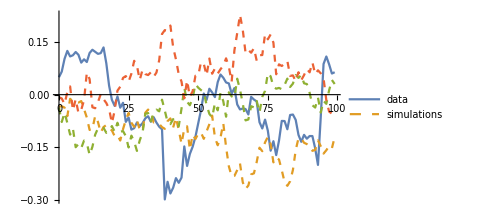

```mathematica
(* Show some simulations and data points *)
showSims=3;
showPoints=100;
Table[ListLinePlot[Join[{selNpℛsPlots[[i]][[;;showPoints]]}, selPaths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,selN}]
```

```mathematica
(* The estimated number of parameters of the sample selections fits: *)
(* From R's loess, using list of (selections) effective dfs: *)
selRInputs="bestSpan <- "<> ToString[bestSpan]<>"\n"<>
"bubbleScaled<-read.csv(\""<>ToString[#]<>"\", sep='\\t', header=TRUE)"<>"\n"<>
"bubble.lo<-loess(value~time, bubbleScaled, degree=1, span=bestSpan)"<>"\n"<>
"pred=predict(bubble.lo, 1, se=TRUE);"<>"\n"<>
"bubble.lo$enp"<>"\n"<>
"pred$df"<>"\n"<>
"sum(bubble.lo$residuals^2)"<>"\n"<>
"bubble.lo$s"<>"\n"<>
"pred$se.fit"&/@selBubbleScaledCsvs;
```

```mathematica
selRRuns=RunProcess[{"/usr/local/bin/R", "--vanilla"}, All, #]&/@selRInputs;
```

```mathematica
(* {Estimated number of params, Degrees of freedom}: *)
selRParams=ToExpression[StringSplit[#][[2]]]&/@StringSplit[#["StandardOutput"], "\n"][[-10;;-8;;2]]&/@selRRuns
```

{{17.6651,1565.77},{17.6324,1494.81},{17.5749,1423.89},{17.8398,1352.54},{17.8104,1281.58},{17.7488,1210.66},{17.6927,1139.74},{17.6207,1067.83},{17.9726,996.372},{17.9063,925.46},{17.8495,854.536},{17.8863,783.489},{17.8054,712.597}}

```mathematica
effectiveDfs
estimatedNParams
(*selEstimatedDfs=Table[Length[selBubbleScaled[[i]]]-estimatedNParams, {i, selN}]*)
selEffectiveDfs=Table[selRParams[[i]][[2]], {i, selN}]
```

1565.77

17.6651

{1565.77,1494.81,1423.89,1352.54,1281.58,1210.66,1139.74,1067.83,996.372,925.46,854.536,783.489,712.597}

```mathematica
(* The "mean" RSSs (RSS/df) of the simulations: *)
selMeanRSSs=Table[Map[Total[(#[[All,2]])^2]/selEffectiveDfs[[i]]&,selPaths[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selMeanRSSs*)
```

```mathematica
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^3.," GB"}];
Needs["Utilities`CleanSlate`"]
memory
```

Memory Used: 1.71537 GB

```mathematica
Remove[selSims]
Remove[selNpℛsPlots]
memory
```

Memory Used: 1.71546 GB

```mathematica
CleanSlate[];
memory
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 241379 Kb

Memory Used: 1.48538 GB

```mathematica
(* The standardized "mean" RSSs: *)
selStdMeanRSSs=Table[Map[#/selStdDevℛs[[i]]&,selMeanRSSs[[i]]], {i, selN}];
(*Histogram[#, ImageSize->Medium]&/@selStdMeanRSSs*)
```

```mathematica
(* Count *)
selCounts=Table[With[{ℛerror= ℛerrors[[i]]},Select[selMeanRSSs[[i]],#>ℛerror &]//Length],{i,selN}]
```

{0,0,0,0,0,0,0,0,0,0,1,0,3}

```mathematica
selPValues=Table[selCounts[[i]]/Length[selMeanRSSs[[i]]], {i, selN}]//N
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.001,0.,0.003}

```mathematica
selRejected=#<(1-0.95)&/@selPValues
```

{True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(* Take the first / largest interval that is not rejected *)
firstNotRejectedIndex=Select[Table[{i,selRejected[[i]]==False},{i,selN}], #[[2]]&]//First//#[[1]]&
```

First::nofirst: {} has zero length and no first element.

{}

```mathematica
(* As a fallback (if all rejected), take the one with the highest non-zero p-value *)
highestPRejected=ReverseSortBy[Select[MapIndexed[{#1, #2[[1]]}&, selPValues], 0< #[[1]]<(1-0.95)&], {#[[1]],-#[[2]]}&];
highestPRejectedIndex=If[Length[highestPRejected]>0, First[highestPRejected][[2]],{}]
```

13

```mathematica
(* As a fallback (if all rejected, and no positive p-values), take the one with the min tc *)
minTc=Min[fits[[;;,6,2]]]
minTcIndex=Select[Table[{i,fits[[i,6,2]]==minTc},{i,selN}],#[[2]]&]//First//#[[1]]&
```

1.71256

1

```mathematica
index=If[NumericQ[firstNotRejectedIndex], firstNotRejectedIndex,If[NumericQ[highestPRejectedIndex], highestPRejectedIndex, minTcIndex]]
```

13

```mathematica
selFit={fits[[index]], "index"-> index}//Flatten
```

{a→1.684,b→-1.26982,c→0.102256,d→-0.215871,T_1→0.537313,tc→1.75734,m→0.1,ω→3.9,RSS→15.8725,ℛerror→0.0147377,ℛσ→0.121062,LL→2360.57,ρ→0.972858,σ→-0.0280011,μ→-9.78502×10^-19,index→13}

```mathematica
bestIndex=index
fit=fits[[bestIndex]]
```

13

{a→1.684,b→-1.26982,c→0.102256,d→-0.215871,T_1→0.537313,tc→1.75734,m→0.1,ω→3.9,RSS→15.8725,ℛerror→0.0147377,ℛσ→0.121062,LL→2360.57,ρ→0.972858,σ→-0.0280011,μ→-9.78502×10^-19}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* Do it over the best params *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.1

3.9

1.75734

2360.57

```mathematica
t1=Subscript[T, 1]/.fit
```

0.537313

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&];
```

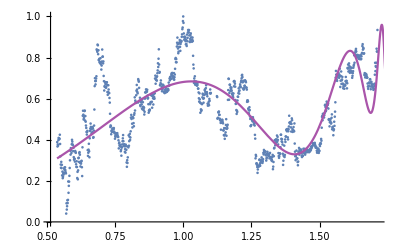

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{colors[[bestIndex]]}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→1.684,b→-1.26982,c→0.102256,d→-0.215871,T_1→0.537313,tc→1.75734,m→0.1,ω→3.9,RSS→15.8725,ℛerror→0.0147377,ℛσ→0.121062,LL→2360.57,ρ→0.972858,σ→-0.0280011,μ→-9.78502×10^-19}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest];
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.972858,σ→-0.0280011,μ→-9.78502×10^-19}

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match. *)
```

```mathematica
(* Now sligthly vary tc, and recompute residuals until the LL is 1.92 times below the max: *)
lowCItc=bestTc;
lowCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/1000;
oldSign=1;
Monitor[While[delta=bestLL-lowCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
lowCItc=lowCItc+ precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest];
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],{delta}]
delta
{lowCItc, bestTc}
```

1.92008

{1.74722,1.75734}

```mathematica
(* Let's do the upper leg of the CI: *)
highCItc=bestTc;
highCILL=bestLL;
```

```mathematica
target=1.92;
epsilon=1/10000;
precision=1/100;
oldSign=-1;
Monitor[While[delta=bestLL-highCILL;Not[target<=delta <target+epsilon],
sign=Sign[delta-target];
highCItc=highCItc- precision sign;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest];
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ];
precision=If[sign!=oldSign,precision /2,precision];
oldSign=sign;
],delta]
delta
{lowCItc, bestTc, highCItc}
```

1.92007

{1.74722,1.75734,1.76648}

```mathematica
(* Dates correction: *)
lastScaledTc=bubbleBest[[-1]][[1]]
```

1.71246

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc/lastScaledTc]
```

Wed 15 Apr 2026 08:38:38

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc/lastScaledTc]
```

Wed 15 Apr 2026 18:08:19

```mathematica
(* And the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc/lastScaledTc]
```

Thu 16 Apr 2026 02:43:40

```mathematica
(* With the mean tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc/lastScaledTc]
```

Tue 14 Apr 2026 09:47:47

```mathematica
(* With the max tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] maxTc/lastScaledTc]
```

Wed 15 Apr 2026 18:08:19

```mathematica
(* With the min tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] minTc/lastScaledTc]
```

Tue 14 Apr 2026 00:05:38

```mathematica
(* For reference: *)
{#[[5]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[5]][[2]]/lastScaledTc],#[[6]],DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] #[[6]][[2]]/lastScaledTc]}&/@fits//TableForm
```

T_1→0. | Fri 6 Feb 2026 00:00:00 | tc→1.71256 | Tue 14 Apr 2026 00:05:38
T_1→0.0447761 | Sat 7 Feb 2026 18:02:41 | tc→1.71256 | Tue 14 Apr 2026 00:05:38
T_1→0.0895522 | Mon 9 Feb 2026 12:05:22 | tc→1.71256 | Tue 14 Apr 2026 00:05:38
T_1→0.134328 | Wed 11 Feb 2026 06:08:03 | tc→1.71256 | Tue 14 Apr 2026 00:05:38
T_1→0.179104 | Fri 13 Feb 2026 00:10:44 | tc→1.71256 | Tue 14 Apr 2026 00:05:38
T_1→0.223881 | Sat 14 Feb 2026 18:13:25 | tc→1.71256 | Tue 14 Apr 2026 00:05:38
T_1→0.268657 | Mon 16 Feb 2026 12:16:07 | tc→1.71256 | Tue 14 Apr 2026 00:05:38
T_1→0.313433 | Wed 18 Feb 2026 06:18:48 | tc→1.71256 | Tue 14 Apr 2026 00:05:38
T_1→0.358209 | Fri 20 Feb 2026 00:21:29 | tc→1.71256 | Tue 14 Apr 2026 00:05:38
T_1→0.402985 | Sat 21 Feb 2026 18:24:10 | tc→1.71256 | Tue 14 Apr 2026 00:05:38
T_1→0.447761 | Mon 23 Feb 2026 12:26:51 | tc→1.75734 | Wed 15 Apr 2026 18:08:19
T_1→0.492537 | Wed 25 Feb 2026 06:29:33 | tc→1.75734 | Wed 15 Apr 2026 18:08:19
T_1→0.537313 | Fri 27 Feb 2026 00:32:14 | tc→1.75734 | Wed 15 Apr 2026 18:08:19

```mathematica
(* Compute market cap at the low leg of the best Tc: *)
bestM=bestLppls[bestTc-epsilon,bestTc]
```

1.08598

```mathematica
lowCIM=bestLppls[lowCItc,bestTc]
```

0.81087

```mathematica
lastScaledM=bubbleBest[[-1]][[2]]
Exp[lastScaledM]
```

0.934188

2.54515

```mathematica
lastPriceDate
```

2026-04-14

```mathematica
(* Closing market cap at lastPriceDate date (`$lastPriceDate`) (https://coinmarketcap.com/currencies/bitcoin/historical-data/https://coinmarketcap.com/currencies/bitcoin/historical-data/Nonehttps://coinmarketcap.com/currencies/bitcoin/historical-data/HyperlinkActionRecycledHyperlinkActive) (Millions of USD): *)
(* Automated download *)
timeStartTs=UnixTime[lastPriceDate];
timeEndTs=timeStartTs+86400;
latestMarketCapUrl="https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart="<>ToString[timeStartTs]<>"&timeEnd="<>ToString[timeEndTs]<>"&interval=1d"
```

https://api.coinmarketcap.com/data-api/v3.1/cryptocurrency/historical?id=1&convertId=2781&timeStart=1776117600&timeEnd=1776204000&interval=1d

```mathematica
latestMarketCapData=Import[latestMarketCapUrl]
```

```mathematica
latestMarketCapInner=Flatten[latestMarketCapData[[1]][[2]][[5]][[2]]]
```

```mathematica
(* Build a list of timeCloses and marketCaps: *)
latestMarketCapWithTime=SortBy[MapThread[{#1, #2[[2]][[7]]}&,{latestMarketCapInner[[2;;-1;;5]], latestMarketCapInner[[5;;-1;;5]]}], First][[-1]]
```

{timeClose→2026-04-14T23:59:59.999Z,marketCap→1.48482276901449×10^12}

```mathematica
latestMarketCap=latestMarketCapWithTime[[2]][[2]]/10^7
```

148482.276901449

```mathematica
(* Plot predicted market cap evolution (USD) :*)
fixDate[brokenDate_]:= StringTake[brokenDate,2]<>"/"<>StringTake[brokenDate,3;;]
ticksH[min_,max_]:=Table[{i,Rotate[fixDate[Block[{$DateStringFormat={"Day","Month","/","YearShort"}},DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]i/lastScaledTc]]], π/3]},{i,{t1,lastScaledTc,lowCItc, bestTc, highCItc}}]
```

```mathematica
ticksVM[min_,max_]:=Table[{i,"$ "<>ToString[IntegerPart[i latestMarketCap/Exp[lastScaledM]]]<>"M"},{i,min, max,1}]
```

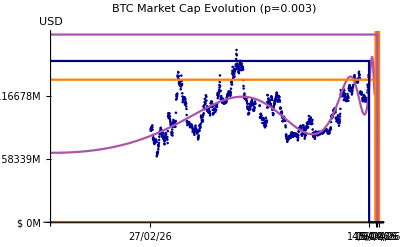

```mathematica
marketCapPrediction=Show[ListPlot[{#[[1]], Exp[#[[2]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Market Cap Evolution (p="<>ToString[selPValues[[index]]]<>")",PlotRange->{{0,maxTc},{0,Exp[bestM]}}, Ticks->{ticksH,ticksVM},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[Exp[lpplsModel/.fit]],UnitStep[ti-lowCItc]Exp[bestM+1],UnitStep[ti-highCItc]Exp[bestM+1]/.fit, UnitStep[lowCItc-ti]Exp[lowCIM],UnitStep[bestTc-ti]Exp[bestM],UnitStep[lastScaledTc-ti]Exp[lastScaledM]}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_MarketCapPrediction-"<>lastPriceDate<>".png",marketCapPrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_MarketCapPrediction-2026-04-14.png

```mathematica
mToMarketCap[m_]:= latestMarketCap/Exp[lastScaledM] Exp[m]
```

```mathematica
lowCIMarketCap=mToMarketCap[lowCIM]
```

131256.

```mathematica
bestMarketCap=mToMarketCap[bestM]
```

172821.

```mathematica
(* The price is the ratio of the market cap (in Millions USD) to the (predicted) supply at the date: *)
mToPrice[m_, date_]:=mToMarketCap[m]10^7/supplyFunction[UnixTime[date]]
```

```mathematica
tcToDate[tc_]:= DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]]tc/lastScaledTc]
tcToDate[lastScaledTc]
```

Tue 14 Apr 2026 00:00:00

```mathematica
(* Check: *)
lastPrice=mToPrice[lastScaledM,tcToDate[lastScaledTc]]
```

74184.

```mathematica
lowCIPrice=mToPrice[lowCIM, tcToDate[lowCItc]]//N
```

65575.3

```mathematica
bestPrice=mToPrice[bestM, tcToDate[bestTc]]
```

86340.2

```mathematica
(* Plot predicted price evolution (USD) :*)
ticksVPrice[min_,max_]:=Table[{i,"$"<>ToString[IntegerPart[i/1000]]<>"K"},{i,min, max,Max[1,IntegerPart[max/100000]]10000}]
ticksVPrice[1, 100000]
```

{{1,$0K},{10001,$10K},{20001,$20K},{30001,$30K},{40001,$40K},{50001,$50K},{60001,$60K},{70001,$70K},{80001,$80K},{90001,$90K}}

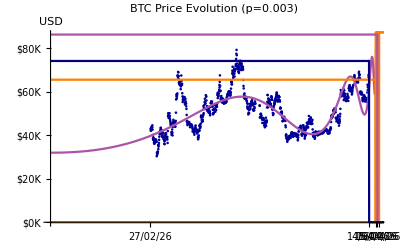

```mathematica
pricePrediction=Show[ListPlot[{#[[1]], mToPrice[#[[2]], tcToDate[#[[1]]]]}&/@bubbleBest, {ImageSize->Full,PlotLabel->"BTC Price Evolution (p="<>ToString[selPValues[[index]]]<>")",PlotRange->{{0,maxTc},{0,bestPrice}}, Ticks->{ticksH,ticksVPrice},PlotStyle->Darker[Blue, .4], TicksStyle->Directive["Label", 10],AxesLabel->"USD"}], Plot[{Evaluate[mToPrice[lpplsModel/.fit, tcToDate[ti]]],UnitStep[ti-lowCItc](bestPrice+1000),UnitStep[ti-highCItc](bestPrice+1000)/.fit, UnitStep[lowCItc-ti]lowCIPrice,UnitStep[bestTc-ti]bestPrice,UnitStep[lastScaledTc-ti]lastPrice}, {ti, 0, maxTc+1/10}, {PlotStyle->{colors[[bestIndex]],Orange, Orange, Orange, colors[[bestIndex]], Darker[Blue, .5]}}]]
```

```mathematica
Export[base <>"png/BTC_PricePrediction-"<>lastPriceDate<>".png",pricePrediction]
```

/Users/mauro/Projects/Bitcoin/png/BTC_PricePrediction-2026-04-14.png